# IN232 Term Paper

## Name: Soumyadeep Sarma, SR No: 20455

```mathematica
ℏ = 1 (*atomic units*);
Ry  = 1 (*rydberg unit of energy*);
```

We solve the secular equation here, and solve for the energy eigenvalues, which give us our dispersion relations. We first write out all the constants in atomic units.

```mathematica
Eg = 1.503*Ry ;
a0 = 4.050  (*in angstrom*);
Ecr = 0.244*Ry ;
Eso = 0.351 *Ry ;
m = 1/2(*atomic units*);
mz = 0.060*m;
mt = 0.075*m;
A1 = -18.39*ℏ^2/(2*m);
A2 = -1.87*ℏ^2/(2*m);
A3 = 17.05*ℏ^2/(2*m);
A4 = -6.26*ℏ^2/(2*m);
A5 = 6.83*ℏ^2/(2*m);
A6 =- 7.27*ℏ^2/(2*m);
```

Next, we write the expressions for all the parameters in terms of these constants (here k_xis labeled as x, k_y as y, k_z as z):

```mathematica
$Assumptions:={x ∈ Reals && y∈ Reals && z ∈ Reals}
```

```mathematica
E1 = Ecr;
E2 = Eso/3;
E3 = Eso/3;
P1 = √(ℏ^2/(2*m)(m/mz-1)((Eg+E1+E2)(Eg+2*E2)-2*E3^2)/(Eg+2*E2));
P2= √(ℏ^2/(2*m)(m/mt-1)(Eg*((Eg+E1+E2)(Eg+2*E2)-2*E3^2))/((Eg+E1+E2)(Eg+E2)-E3^2));
Ec = Eg + E1;
k = √(x^2+y^2+z^2);
λ = A1*z^2+A2*(x^2+y^2);
θ = A3*z^2+A4*(x^2+y^2);
F = E1+E2+λ + θ;
G = E1-E2+λ + θ;
L= A5*(x+ⅈ*y)^2;
H = A6*(x+ⅈ*y)*z;
Es = √2*E3;
k1 = -(x+ⅈ*y)*P2/(√2);
k2 = (x-ⅈ*y)*P2/(√2);
k3 = z*P1;
```

We now form the 8 by 8 matrix as given in Ref. 2 of the paper as:

```mathematica
Hmat = ({{Ec+(ℏ^2*k^2)/(2*m), k1, k2, k3, 0, 0, 0, 0}, {-k2, F, -L*, -H*, 0, 0, 0, 0}, {-k1, -L, G, H, 0, 0, 0, Es}, {k3, H, -H*, λ, 0, 0, Es, 0}, {0, 0, 0, 0, Ec+(ℏ^2*k^2)/(2*m), k2, k1, k3}, {0, 0, 0, 0, -k1, F, -L, H}, {0, 0, 0, Es, -k2, -L*, G, -H*}, {0, 0, Es, 0, k3, H*, -H, λ}});
```

```mathematica
v =Eigenvalues[Hmat]//FullSimplify
```

```mathematica
(v/.{x->0.02,y->0,z->0})(*checking for values*)
```

{-0.112861,-0.112861,0.241392,0.241392,0.361395,0.361395,1.75273,1.75273}

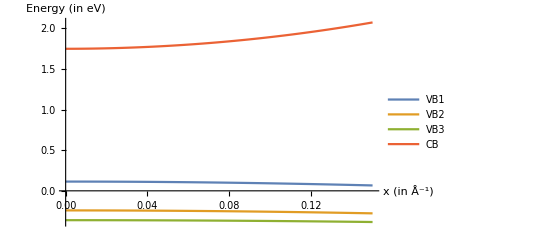

```mathematica
Plot[{-(v/.{y->0,z->0})[[1]],-(v/.{y->0,z->0})[[3]],-(v/.{y->0,z->0})[[5]],(v/.{y->0,z->0})[[7]]},{x,0,0.15},PlotLegends->{"VB1","VB2","VB3","CB"},AxesLabel->{"x (in Å^-1)","Energy (in eV)"}] (*As bands are doubly degerenerate*)
```

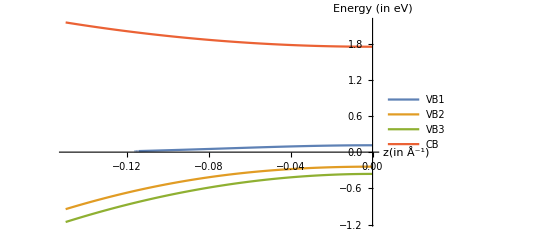

```mathematica
Plot[{-(v/.{x->0,y->0})[[1]],-(v/.{x->0,y->0})[[3]],-(v/.{x->0,y->0})[[5]],(v/.{x->0,y->0})[[7]]},{z,0,-0.15}, PlotLegends->{"VB1","VB2","VB3","CB"},AxesLabel->{"z(in Å^-1)","Energy (in eV)"}] (*Expression has even powers only, so does not matter*)
```

```mathematica
FG[k_]:=If[k<=0, -(v/.{y->0,z->0 , x->k}), -(v/.{x->0,y->0, z->k})]
```

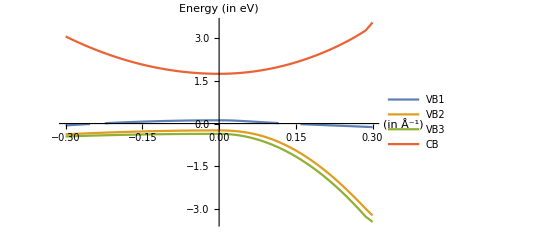

```mathematica
Plot[{FG[k][[1]],FG[k][[3]],FG[k][[5]],-FG[k][[7]]},{k,-0.30,+0.30}, PlotLegends->{"VB1","VB2","VB3","CB"},AxesLabel->{"(in Å^-1)","Energy (in eV)"}] (*Expression has even powers only, so does not matter*)
```

Here, the +-ve x-axis corresponds to the x-direction (k_x), while the -ve x-axis corresponds to the z-direction (k_z). Clearly, as we described in the paper, there is a sharp change in the line shapes of the valence bands. This is the plot present in the term paper.